### Plot Options

```mathematica
SetOptions[{Plot, ListPlot, ListLinePlot, ListLogPlot, ListLogLogPlot}, 
{BaseStyle -> {FontFamily -> "Times", FontSize -> 20}, PlotStyle -> ColorData[108, "ColorList"], PlotRange -> All, Frame -> True, GridLines -> Automatic, PlotLegends -> "Expressions", ImageSize -> 350}];
SetOptions[{ListDensityPlot}, {LabelStyle -> {FontFamily -> "Times", FontSize -> 20}, Frame -> True, FrameLabel-> {"t (ns)"}, PlotRange -> All, PlotLegends -> True, ColorFunction->ColorData["SunsetColors"], ColorFunctionScaling->True, ImageSize -> 350}];
```

## Start up

### Principle quantum number n for evaluation

```mathematica
n = 30;
R = Table[r, {r, 0.5n^2, 2.4n^2, 1.9n^2/600}];
Θ = Table[θ, {θ, 0, π, π/32}];
```

### Electronic wave functions

#### Radial hydrogenic wave function

```mathematica
Rhyd[l_, r_] := Sqrt[(2/n)^3 ((n-l-1)!/(2*n*(n+l)!))] Exp[-r/n] (2r/n)^l LaguerreL[n-l-1,2l+1,2r/n]
```

#### Angular wave function

```mathematica
Y[l_,m_,θ_] := Sqrt[(2l+1)/(4π)] Sqrt[Gamma[l-m+1]/Gamma[l+m+1]] LegendreP[l,m,Cos[θ]]
```

#### Vector of wave functions

```mathematica
wfTable[r_] := Flatten[Table[If[m==0, Rhyd[l,r] Y[l,0,0], 0], {l,0,n-1}, {m,-l,l}]]
wfTable[r_,θ_] := Flatten[Table[Rhyd[l,r] Y[l,m,θ], {l,0,n-1}, {m,-l,l}]]
vec[r_,θ_] := If[θ==0, wfTable[r], wfTable[r,θ]]
```

### Scattering interaction

#### Semi-classical electron wave number

```mathematica
k[r_] := Sqrt[2(-(2n^2)^(-1)+1/r)];
```

#### Energy dependent scattering length (finite range theory)

```mathematica
A[r_] := -16.1+π/3 319.2Re[k[r]];
```

### The trilobite potential

```mathematica
T[r_] := Sum[(2l+1)/(4π)Rhyd[l,r]^2, {l,0,n-1}]
```

```mathematica
TRIL = Table[{r,T[r]}, {r,R}]; // AbsoluteTiming
VEC = Table[With[{tt=vec[r,0]},{r,tt.tt}], {r,R}]; // AbsoluteTiming
```

{1.14076,Null}

{1.90945,Null}

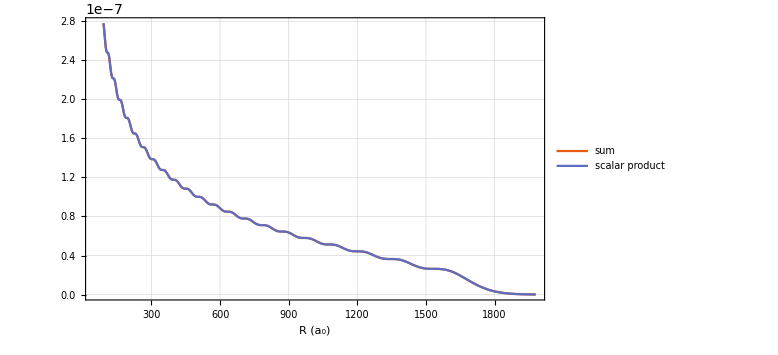

```mathematica
ListLinePlot[{TRIL,VEC}, PlotLegends->{"sum", "scalar product"}]
```

```mathematica
Tint = Interpolation[Table[{r,T[r]}, {r,R}], "ExtrapolationHandler" -> {0 &, "WarningMessage" -> False}];
```

#### Timing tests

```mathematica
Ttest1[r_,θ_] := Sum[Rhyd[l,r]^2 Y[l,m,θ]^2, {l,0,n-1}, {m,-l,l}]
Ttest2[r_,θ_] := With[{tt=vec[r,θ]},tt.tt]
```

```mathematica
θ0 = π/4;
Ttest1[1.8n^2,θ0];//AbsoluteTiming
Ttest2[1.8n^2,θ0];//AbsoluteTiming
```

{0.936484,Null}

{0.872334,Null}

#### Matrix of trilobite basis states

```mathematica
Tmat[r_,θ_]:=(
a=vec[r,θ];
Outer[Times,a,a])
```

### Angular Integrals

#### ⟨ l m | cos(θ) | l' m' ⟩

```mathematica
CosLM[li_,lj_,mi_,mj_]:=If[mi==mj && Abs[li-lj]==1, With[{l=Min[li,lj]}, Sqrt[(l+mi+1)(l-mi+1)/(2l+1)/(2l+3)]], 0]
```

#### ⟨ l m | sin (θ) cos (ϕ) | l' m' ⟩

```mathematica
SinCosLM[li_,lj_,mi_,mj_]:=Which[
Abs[mi-mj]≠1 || Abs[li-lj]≠1,0,
mi+1==mj && li-1==lj, Sqrt[(li-mi)(li-mi-1)/(4li^2-1)],
mi-1==mj && li-1==lj, -Sqrt[(li+mi)(li+mi-1)/(4li^2-1)],
mi+1==mj && li+1==lj, Sqrt[(2li+1)(li+mi+2)/(2li+3)/(li+mi+1)]((li-mi)/(2li+1)-1),
mi-1==mj && li+1==lj,  -Sqrt[(2li+1)(li-mi+2)/(2li+3)/(li-mi+1)]((li+mi)/(2li+1)-1)
]/2
```

#### ⟨ l m | sin (θ) sin (ϕ) | l' m' ⟩

```mathematica
SinSinLM[li_,lj_,mi_,mj_]:=Which[
Abs[mi-mj]≠1 || Abs[li-lj]≠1,0,
mi+1==mj && li-1==lj, Sqrt[(li-mi)(li-mi-1)/(4li^2-1)],
mi-1==mj && li-1==lj, -Sqrt[(li+mi)(li+mi-1)/(4li^2-1)],
mi+1==mj && li+1==lj, Sqrt[(2li+1)(li+mi+2)/(2li+3)/(li+mi+1)]((li-mi)/(2li+1)-1),
mi-1==mj && li+1==lj,  -Sqrt[(2li+1)(li-mi+2)/(2li+3)/(li-mi+1)]((li+mi)/(2li+1)-1)
]/2/I
```

#### ⟨ l m | sin.b2 (θ) | l' m' ⟩

```mathematica
SinSqLM[li_,lj_,mi_,mj_]:=Which[
Abs[mi-mj]≠0 ,0,
li==lj, 2(li^2+li+1+mi^2)/((2li+3)(2*li-1)),
Abs[li-lj]==2, With[{l=Min[li,lj]}, Sqrt[((l+2)^2-mi^2)((l+1)^2-mi^2)/((2l+5)(2l+3)^2 (2li+1))]]]
```

#### Matt's sin.b2 (θ) term

```mathematica
sinsq[l1_,l2_,m1_,m2_]:=If[m1≠m2,0,If[l1==l2,-Sqrt[5]*(-1)^m1*Sqrt[(2l1+1)(2l2+1)*1/4/Pi]*ThreeJSymbol[{l1,0},{l2,0},{0,0}]*ThreeJSymbol[{l1,-m1},{l2,m2},{0,0}]+(-1)^m1*Sqrt[(2l1+1)(2l2+1)*5/4/Pi]*ThreeJSymbol[{l1,0},{l2,0},{2,0}]*ThreeJSymbol[{l1,-m1},{l2,m2},{2,0}],If[l1==l2-2||l1==l2+2,(-1)^m1*Sqrt[(2l1+1)(2l2+1)*5/4/Pi]*ThreeJSymbol[{l1,0},{l2,0},{2,0}]*ThreeJSymbol[{l1,-m1},{l2,m2},{2,0}],0],0]]/(-3/4 √(5/Pi))
```

### Radial Integral

#### ⟨ n l | r^j | n' l' ⟩

```mathematica
RtoJ[li_, lj_, j_]:=4 2^(li+lj)/n^(li+2)/n^(lj+2) Sqrt[(n-li-1)! (n-lj-1)!/(n+li)!/(n+lj)!] Sum[(-2)^(mi+mj)/mi!/mj!/n^mi/n^mj*(j+li+lj+mi+mj+2)!/(2/n)^(j+3+li+lj+mi+mj) Binomial[n+li,n-li-mi-1] Binomial[n+lj,n-lj-mj-1],{mi,0,n-li-1},{mj,0,n-lj-1}]
```

### E - field matrix

#### | l m ⟩

```mathematica
lm = Flatten[Table[{l,m}, {l,0,n-1}, {m,-l,l}],1];
```

#### ⟨ n l m | E z | n l' m'⟩

```mathematica
Ez = Table[If[Abs[lm[[i,1]]-lm[[j,1]]]==1 && lm[[i,2]]==lm[[j,2]], RtoJ[lm[[i,1]],lm[[j,1]],1] CosLM[lm[[i,1]],lm[[j,1]],lm[[i,2]],lm[[j,2]]], 0], {i,1,Length[lm]}, {j,1,Length[lm]}]; // AbsoluteTiming
```

{6.79033,Null}

#### ⟨ n l m | E x | n l' m'⟩

```mathematica
Ex = Table[If[Abs[lm[[i,1]]-lm[[j,1]]]==1 && Abs[lm[[i,2]]-lm[[j,2]]]==1, RtoJ[lm[[i,1]],lm[[j,1]],1] SinCosLM[lm[[i,1]],lm[[j,1]],lm[[i,2]],lm[[j,2]]], 0], {i,1,Length[lm]}, {j,1,Length[lm]}]; // AbsoluteTiming
```

{12.2455,Null}

```mathematica
Efield[θ_] := Cos[θ] Ez+Sin[θ] Ex
```

### Trilobite dipole moment

```mathematica
dmT[r_] := (
a=vec[r,0];
b=Ez.a;
c=T[r];
a.b/c)
```

```mathematica
DMT = Table[{r,dmT[r]}, {r,R}]; // AbsoluteTiming
cDMT = Table[{r,r-n^2/2}, {r,R}]; // AbsoluteTiming
```

{82.4177,Null}

{0.000273,Null}

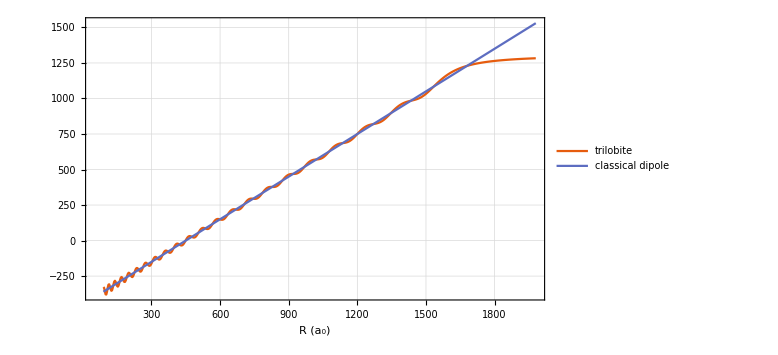

```mathematica
ListLinePlot[{DMT, cDMT}, PlotLegends->{"trilobite", "classical dipole"}]
```

```mathematica
dmTint = Interpolation[Table[{r,dmT[r]}, {r,R}]];
```

### Linear dipole in an electric field

```mathematica
DinE[r_,θ_] := (r-n^2/2) Cos[θ]
TinE[r_,θ_] := dmT[r] Cos[θ]
```

```mathematica
TinEtest1[r_,θ_] := (
a=vec[r,0];
b=Efield[θ].a;
c=T[r];
a.b/c)

TinEtest2[r_,θ_] := (
a=vec[r,θ];
b=Ez.a;
c=T[r];
a.b/c)
```

```mathematica
r0 = 1800;
dip1 = Table[{θ,DinE[r0,θ]}, {θ,Θ}]; // AbsoluteTiming
dip2 = Table[{θ,TinEtest1[r0,θ]}, {θ,Θ}]; // AbsoluteTiming
dip3 = Table[{θ,TinEtest2[r0,θ]}, {θ,Θ}]; // AbsoluteTiming
dip4 = Table[{θ,TinE[r0,θ]}, {θ,Θ}]; // AbsoluteTiming
```

{0.000368,Null}

{33.4864,Null}

{138.817,Null}

{4.77422,Null}

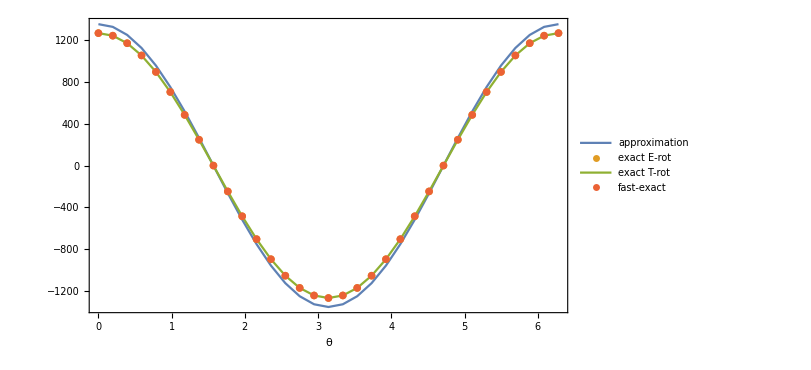

```mathematica
ListPlot[{dip1,dip2,dip3,dip4}, Joined->{True,False,True,False}, PlotLegends->{"approximation", "exact E-rot",  "exact T-rot", "fast-exact"}, FrameLabel->{"θ"}]
```

### Exportation

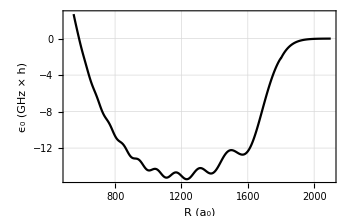

```mathematica
tplot = ListLinePlot[{Table[{r,2π Quiet[Tint[r]]A[r] Aunit},{r,550,2100,1}]}, FrameLabel->{"R (a_0)", "ϵ_0 (GHz × h)"}, PlotStyle->Black]
```

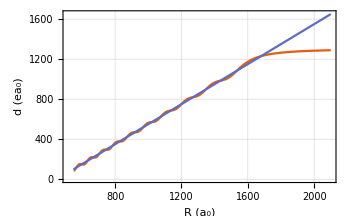

```mathematica
dplot = ListLinePlot[{Table[{r,Quiet[dmTint[r]]},{r,550,2100,1}], Table[{r,r-n^2/2},{r,550,2100,1}]}, FrameLabel->{"R (a_0)", "d (ea_0)"}]
```

```mathematica
Export["/home/fhummel/Documents/Wolfram Mathematica/efield/tril.pdf", tplot];
Export["/home/fhummel/Documents/Wolfram Mathematica/efield/dipo.pdf", dplot];
```

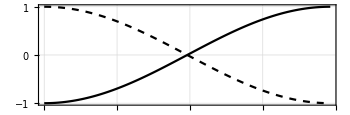

```mathematica
zplot = ListLinePlot[Table[{{θ,-Cos[θ]},{θ,Cos[θ]}},{θ,0,π,0.01π}]ᵀ, PlotStyle->{Black,{Black,Dashed}}, AspectRatio->1/3]
```

```mathematica
Export["/home/fhummel/Documents/paper/efield/plots/TrilobiteAngularLoc.pdf", zplot];
```

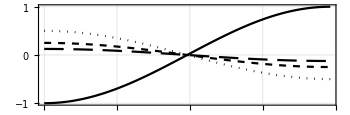

```mathematica
zplot = ListLinePlot[Table[{{θ,-Cos[θ]},{θ,Cos[θ]/8},{θ,Cos[θ]/4},{θ,Cos[θ]/2}},{θ,0,π,0.01π}]ᵀ, PlotStyle->{Black, {Black,Dashing[{0.04,0.02}]},{Black,Dashed}, {Black,Dotted}}, AspectRatio->1/3]
```

```mathematica
Export["/home/fhummel/Documents/paper/efield/plots/TrilobiteAngularLoc_new.pdf", zplot];
```

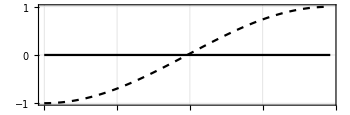

```mathematica
zplot = ListLinePlot[Table[{{θ,-Cos[θ]},{θ,0}},{θ,0,π,0.01π}]ᵀ, PlotStyle->{{Black,Dashed}, Black}, AspectRatio->1/3]
```

```mathematica
Export["/home/fhummel/Documents/paper/efield/plots/TrilobiteAngularIso.pdf", zplot];
```

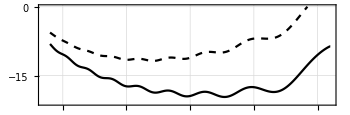

```mathematica
zplot = ListLinePlot[Table[{r,PES[r,π,i]},{i,{-400,400}},{r,700,1800,1}], PlotRange->{-21,0}, PlotStyle->{{Black,Dashed},Black}, AspectRatio->1/3]
```

```mathematica
Export["/home/fhummel/Documents/paper/efield/plots/TrilobiteRadialLoc400.pdf", zplot];
```

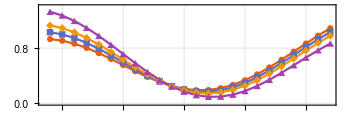

```mathematica
zplot = ListLinePlot[Table[{r,15.6+i/100+PES[r,π,i]},{i,{0,100,200,400}},{r,1170,1285,5}], AspectRatio->1/3, PlotRange->{0,1.4}, PlotMarkers->Automatic, PlotLegends->{"0", "100", "200", "400"}]
```

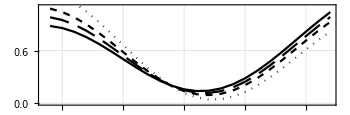

```mathematica
zplot = ListLinePlot[Table[{r,15.55+i/100+PES[r,π,i]},{i,{0,100,200,400}},{r,1170,1285,5}], AspectRatio->1/3, PlotRange->{0,1.1}, PlotStyle->{Black, {Black,Dashing[{0.04,0.02}]},{Black,Dashed}, {Black,Dotted}}, PlotLegends->{"0", "100", "200", "400"}]
```

```mathematica
Export["/home/fhummel/Documents/paper/efield/plots/TrilobiteRadialIso.pdf", zplot];
```

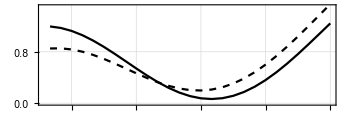

```mathematica
zplot = ListLinePlot[Table[{r,15+i/85+PES[r,π,i]},{i,{400,50}},{r,1310,1440,5}], AspectRatio->1/3, PlotRange->{0,1.5}, PlotStyle->{Black,{Black,Dashed}}, PlotLegends->{"400","50"}]
```

```mathematica
Export["/home/fhummel/Documents/paper/efield/plots/TrilobiteRadialLoc.pdf", zplot];
```

## Electronic solutions

### Trilobite potentials in an electric field

```mathematica
Aunit = 2 3.289841960355 10^6;
Eunit = 5.14220674763 10^11;
```

```mathematica
R1 = Table[r, {r, 0.6n^2, 2.1n^2, 1.5n^2/100}];
PES[r_,θ_,E_] := (2π A[r] Tint[r]+dmTint[r] Cos[θ] E/Eunit) Aunit
```

```mathematica
E0 = 200;
pesrθ = Flatten[Table[{r,θ,PES[r,θ,E0]},{r,R1},{θ,Θ}],1]; // AbsoluteTiming
```

{0.08018,Null}

```mathematica
twodplot = ListPlot3D[pesrθ,PlotRange->{-12,-18}, AxesLabel->{"R (a_0)", "θ", "ϵ (GHz × h)"}, ColorFunction->"Aquamarine",ColorFunctionScaling->False,ViewPoint->{-π/4,π,π/2}, LabelStyle -> {FontFamily -> "Times", FontSize -> 20}, ImageSize->450]
```

-Graphics3D-

```mathematica
Export["/home/fhummel/Documents/Wolfram Mathematica/efield/2D.pdf", twodplot];
```

### Full Diagonalization

```mathematica
FullDiagTrot[r_,θ_,E_] := Eigenvalues[(2π A[r] Tmat[r,θ]+Ez E/Eunit) Aunit, 1]
FullDiagErot[r_,θ_,E_] := Eigenvalues[(2π A[r] Tmat[r,0.]+Efield[θ] E/Eunit) Aunit, 1]
```

{0.001996,Null}

{77.2651,Null}

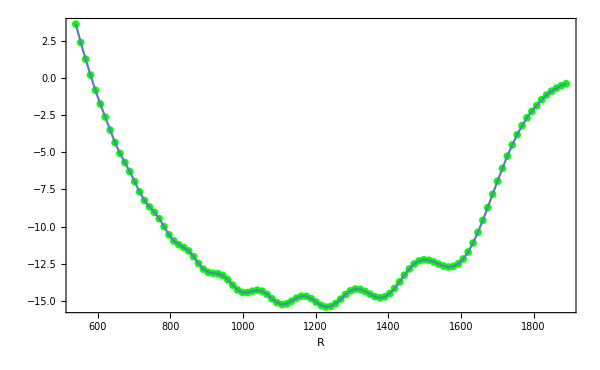

```mathematica
E0 = 0.;
θ0 = 0.;
pes = Table[PES[r,θ0,E0],{r,R1}]; // AbsoluteTiming
pesFDT = Table[FullDiagTrot[r,θ0,E0],{r,R1}];  // AbsoluteTiming
Show[ListPlot[{R1,pes}ᵀ, PlotStyle->Green],
ListLinePlot[{R1,Flatten[pesFDT]}ᵀ]]
```

{0.002192,Null}

{79.2455,Null}

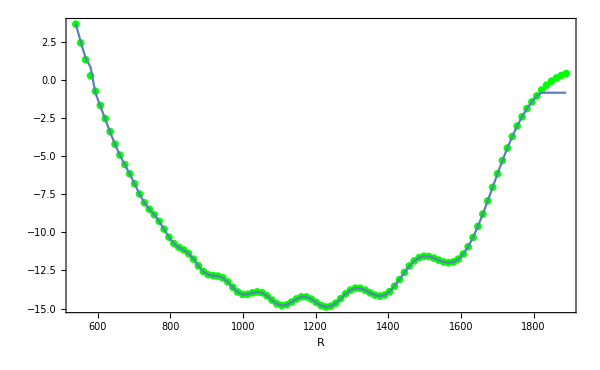

```mathematica
E0 = 50;
θ0 = 0.;
pes = Table[PES[r,θ0,E0],{r,R1}]; // AbsoluteTiming
pesFDT = Table[FullDiagTrot[r,θ0,E0],{r,R1}];  // AbsoluteTiming
Show[ListPlot[{R1,pes}ᵀ, PlotStyle->Green],
ListLinePlot[{R1,Flatten[pesFDT]}ᵀ]]
```

{0.001936,Null}

{91.0077,Null}

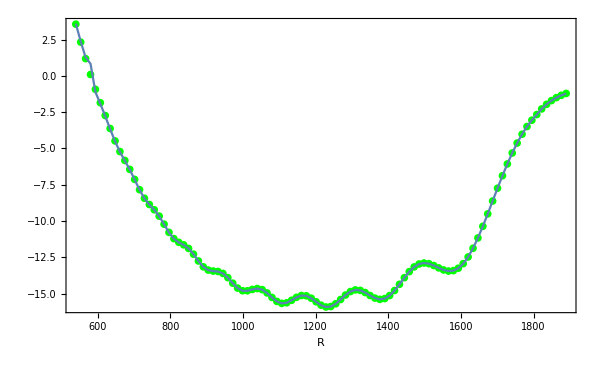

```mathematica
E0 = 50;
θ0 = N[π];
pes = Table[PES[r,θ0,E0],{r,R1}]; // AbsoluteTiming
pesFDT = Table[FullDiagTrot[r,θ0,E0],{r,R1}];  // AbsoluteTiming
Show[ListPlot[{R1,pes}ᵀ, PlotStyle->Green],
ListLinePlot[{R1,Flatten[pesFDT]}ᵀ]]
```

{0.002105,Null}

{75.8103,Null}

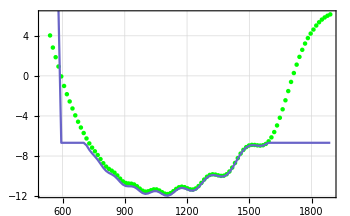

```mathematica
E0 = 400;
θ0 = 0.;
pes = Table[PES[r,θ0,E0],{r,R1}]; // AbsoluteTiming
pesFDT = Table[FullDiagTrot[r,θ0,E0],{r,R1}];  // AbsoluteTiming
Show[ListPlot[{R1,pes}ᵀ, PlotStyle->Green],
ListLinePlot[{R1,Flatten[pesFDT]}ᵀ]]
```

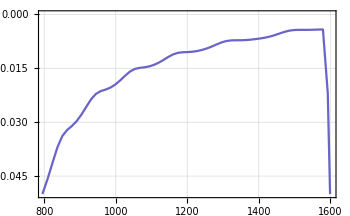

```mathematica
ListLinePlot[{R1,pes/Flatten[pesFDT]-1}ᵀ, PlotRange->{{800,1600},{-0.05,0}}]
```

{0.001748,Null}

{90.5258,Null}

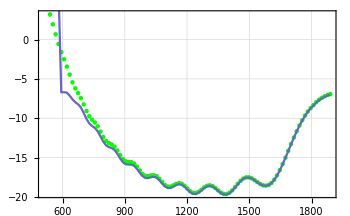

```mathematica
E0 = 400;
θ0 = N[π];
pes = Table[PES[r,θ0,E0],{r,R1}]; // AbsoluteTiming
pesFDT = Table[FullDiagTrot[r,θ0,E0],{r,R1}];  // AbsoluteTiming
Show[ListPlot[{R1,pes}ᵀ, PlotStyle->Green],
ListLinePlot[{R1,Flatten[pesFDT]}ᵀ]]
```

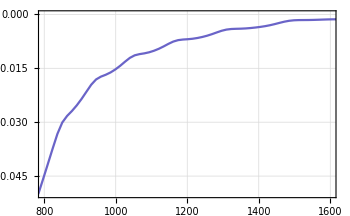

```mathematica
ListLinePlot[{R1,pes/Flatten[pesFDT]-1}ᵀ, PlotRange->{{800,1600},{-0.05,0}}]
```

## Radial Solutions

#### Grid parameters

```mathematica
grid = Table[r, {r, 0.6n^2, 2.1n^2, 1.5n^2/1000}];
L=grid[[-1]]-grid[[1]];
gridpoints=Length[grid];
gridstep =N[L/(gridpoints-1)];
```

#### Hamiltonian

```mathematica
u = 1822.888486192; (*u in m_e*)
M = 86.909180527; (*mass of 87^Rb in u*)
mass = u M/2; (*reduced mass*)
hop = -1/(2 mass gridstep^2);ons=-2 hop;
TridiagMat[n_,{ons_,hop_}]:=SparseArray[{Band[{1,1}]->ons,Band[{2,1}]->hop,Band[{1,2}]->hop},{n,n}]
H0=TridiagMat[gridpoints,{ons,hop}];
Jpot[J_] := J(J+1)/2/grid^2/mass
Shift = -5000 IdentityMatrix[gridpoints];
nstates=100;
```

#### Stationary Solutions

```mathematica
RadSol[J_,θ_,E_] := (
pot = Interpolation[Table[{r,PES[r,θ,E]/Aunit},{r,grid}]];
V=DiagonalMatrix[Jpot[J]+pot[grid]];
H=N[Shift+H0+V];
EigSys=Eigensystem[H,nstates];
Vals=(Sort[EigSys[[1]]]+5000) Aunit;
Vecs=EigSys[[2]][[Ordering[EigSys[[1]]]]];
{Vals, Vecs, Diagonal[V]})
```

#### Vibrational States

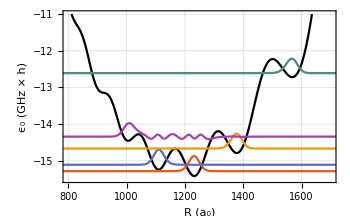

```mathematica
Sol = RadSol[0,0,0];
pecplot = ListLinePlot[{grid,Sol[[3]] Aunit}ᵀ, PlotStyle->Black, PlotRange->{{800,1700},{-15.5,-11}}, FrameLabel->{"R (a_0)","ϵ_0 (GHz × h)"} ];
eigplot = ListLinePlot[Evaluate@Table[{grid,Sol[[1,i]]+2Sol[[2,i]]}ᵀ, {i,{1,2,7,12,38}}]];
vplot = Show[pecplot,eigplot]
```

```mathematica
Export["/home/fhummel/Documents/Wolfram Mathematica/efield/vib.pdf", vplot];
```

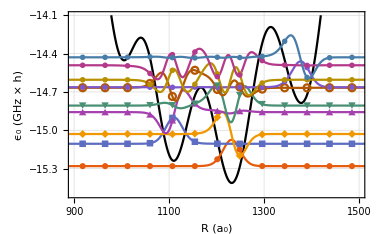

```mathematica
pecplot = ListLinePlot[{grid,Sol[[3]] Aunit}ᵀ, PlotStyle->Black, PlotRange->{{900,1500},{-15.5,-14.1}}, FrameLabel->{"R (a_0)","ϵ_0 (GHz × h)"}, FrameTicks->{{Automatic,None},{{900,1100,1300,1500},None}} ];
eigplot = ListLinePlot[Evaluate@Table[{grid,Sol[[1,i]]+Sol[[2,i]]}ᵀ, {i,10}]];
eigplot2 = ListPlot[Evaluate@Table[{grid,Sol[[1,i]]+Sol[[2,i]]}ᵀ[[1;;-1;;35]], {i,10}], PlotMarkers->Automatic];
vplot = Show[pecplot,eigplot, eigplot2, ImageSize->380]
```

```mathematica
Export["/home/fhummel/Documents/paper/efield/plots/TrilobiteRadialEig.pdf", vplot];
```

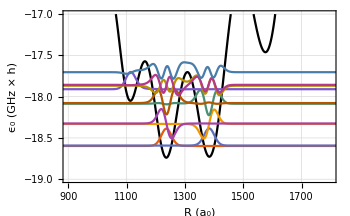

```mathematica
Sol = RadSol[0,π,325];
pecplot = ListLinePlot[{grid,Sol[[3]] Aunit}ᵀ, PlotStyle->Black, PlotRange->{{900,1800},{-19,-17}}, FrameLabel->{"R (a_0)","ϵ_0 (GHz × h)"}, FrameTicks->{{Automatic,None},{{900,1100,1300,1500,1700},None}} ];
eigplot = ListLinePlot[Evaluate@Table[{grid,Sol[[1,i]]+Sol[[2,i]]}ᵀ, {i,10}]];
vplot = Show[pecplot,eigplot]
```

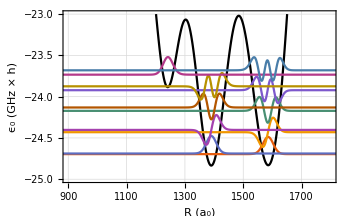

```mathematica
Sol = RadSol[0,π,825];
pecplot = ListLinePlot[{grid,Sol[[3]] Aunit}ᵀ, PlotStyle->Black, PlotRange->{{900,1800},{-25,-23}}, FrameLabel->{"R (a_0)","ϵ_0 (GHz × h)"}, FrameTicks->{{Automatic,None},{{900,1100,1300,1500,1700},None}} ];
eigplot = ListLinePlot[Evaluate@Table[{grid,Sol[[1,i]]+Sol[[2,i]]}ᵀ, {i,10}]];
vplot = Show[pecplot,eigplot]
```

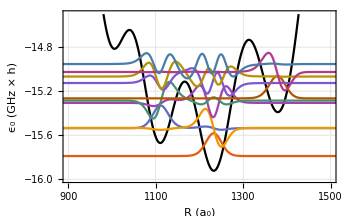

```mathematica
Sol = RadSol[0,π,50];
pecplot = ListLinePlot[{grid,Sol[[3]] Aunit}ᵀ, PlotStyle->Black, PlotRange->{{900,1500},{-16,-14.5}}, FrameLabel->{"R (a_0)","ϵ_0 (GHz × h)"}, FrameTicks->{{Automatic,None},{{900,1100,1300,1500},None}} ];
eigplot = ListLinePlot[Evaluate@Table[{grid,Sol[[1,i]]+Sol[[2,i]]}ᵀ, {i,10}]];
vplot = Show[pecplot,eigplot]
```

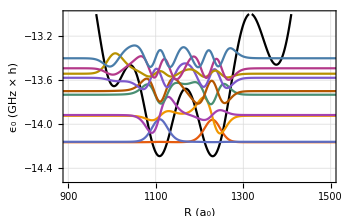

```mathematica
Sol = RadSol[0,0,110];
pecplot = ListLinePlot[{grid,Sol[[3]] Aunit}ᵀ, PlotStyle->Black, PlotRange->{{900,1500},{-14.5,-13}}, FrameLabel->{"R (a_0)","ϵ_0 (GHz × h)"}, FrameTicks->{{Automatic,None},{{900,1100,1300,1500},None}} ];
eigplot = ListLinePlot[Evaluate@Table[{grid,Sol[[1,i]]+Sol[[2,i]]}ᵀ, {i,10}]];
vplot = Show[pecplot,eigplot]
```

#### Naive spectrum

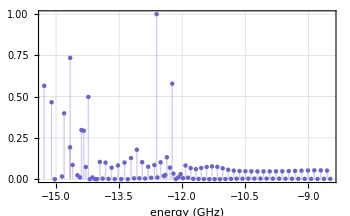

```mathematica
heights=Table[Abs[Total[grid Sol[[2,i]]]]^2,{i,1,nstates}];
heights=heights/Max[heights];
ListPlot[{Sol[[1]],heights}ᵀ,Filling->Axis, FrameLabel->{"energy (GHz)"}]
```

## Field dependences

### angular localization

```mathematica
t = {34,24,20,17};
f= {100,200,300,400};
```

```mathematica
data = {f,t}ᵀ;
lm=NonlinearModelFit[data,a/Sqrt[x],{a},x]
```

FittedModel[340.884/(√x)]

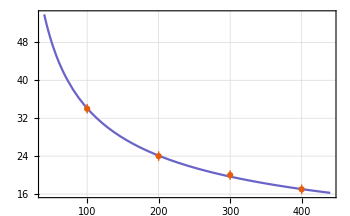

```mathematica
Show[Plot[lm[x],{x,40,440}],ListPlot[{{f,Around[t,1]}ᵀ}]]
```

### radial localization

```mathematica
f={0,100,200,400};
r={1233,1234,1236,1238};
```

```mathematica
data = {f,r}ᵀ;
lm=LinearModelFit[data,x,x]
```

FittedModel[1233.+0.0128571 x]

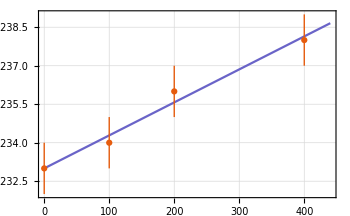

```mathematica
Show[Plot[lm[x],{x,0,440}],ListPlot[{{f,Around[r,1]}ᵀ}]]
```